# Lecture 12 - Oscillations

### A Puzzle...

Differential equations appear all the time in physics (in fact, every equation F=m a we have written has been a differential equation in x, since a=(ⅆ^2 x)/(ⅆ t^2)). In this class, knowledge of differential equations is optional (although assumed); this means that for this course you can simply double check that each solution to a differential equation presented to you actually works, and you will not need to solve any new differential equations in an exam. However, differential equations show up time and again in every field, so learning some tricks will be highly beneficial.

Differential Equation Boot Camp
Find the most general solution to the follow differential equation. Assume a, b, and c are constants that do not depend on x.
1. y'[x]=a
2. y'[x]=a y[x]
3. y'[x]=a y[x]+b
4. a y''[x]+b y'[x]+c y[x]=0

Solution
Our purpose here is to show you some basic tricks used to solve differential equations. We discuss a more rigorous framework in the Differential Equations section below.

1. Integrating both sides yields y[x]=a x+c_0 where c_0 is an arbitrary constant. Note that the differential equation has degree 1 (i.e. the highest derivative which appears in the equation is the first derivative) and that there is 1 arbitrary constant in our solution. When these two numbers match, you have found the most general solution for the differential equation.

2. Rewrite y'[x]=ⅆy/ⅆx and multiply both sides by ⅆx/y to obtain

ⅆy/y=a ⅆx

Integrating yields

Log[y]=a x+c_0

or equivalently

y[x]=c_1 ⅇ^(a x)

where c_1=ⅇ^c_0 is an arbitrary constant. The differential equation has order 1, and our solution has 1 arbitrary constant c_1, so we have found the most general solution.

3. From Part 2, we know that if b=0, we know the solution would be y[x]=c_1 ⅇ^(a x). What if we tried adding a constant C to this solution,

y_guess[x]=c_1 ⅇ^(a x)+C

Substituting this back into the differential equation,

c_1 a ⅇ^(a x)=ⅆy_guess[x]/ⅆx=a y_guess[x]+b=a (c_1 ⅇ^(a x)+C)+b

This equation will be satisfied if C=-b/a, so that the full solution is given by

y[x]=c_1 ⅇ^(a x)-b/a

Note that differential equation has order 1, and our solution has 1 arbitrary constant c_1, so we have found the most general solution. Taking a known solution and adding a constant to it is often a useful trick.

4. Based on Part 2, we might guess that the solution will be in the form of an exponential function, y_guess[x]=C ⅇ^(m x). Substituting into the differential equation,

a C m^2 ⅇ^(m x)+b C m ⅇ^(m x)+c C ⅇ^(m x)=0

Factoring out the C ⅇ^(m x),

a m^2+b m+c=0

which is a simple quadratic equation in terms of m which has the two solutions

m=(-b±√(b^2-4a c))/(2a)

Note that the C canceled, which means that it is a free parameter in each of our two solutions. Therefore, the most general solution to the differential equation equals

y[x]=c_1 ⅇ^((-b+√(b^2-4a c))/(2a)x)+c_2 ⅇ^((-b-√(b^2-4a c))/(2a)x)

This time the differential equation has order 2 (since it features (ⅆ^2 y)/(ⅆ x^2)), and our solution has 2 arbitrary constants c_1 and c_2, so we have found the most general solution. □

### Rotation Wrap Up

#### Race to the Finish!

Example
Four objects - a hollow cylinder, a solid cylinder, a hollow sphere, and a solid sphere - are placed on top of an incline and released from rest. In what order will the objects cross the finish line?

```mathematica
centerPlot@-Graphics3D-
```

-Graphics3D-

Solution
We seem to be missing a lot of information. For example, we do not know the masses or radii of any of the objects, nor do we know the angle θ of the incline. Therefore, these quantities must ultimately cancel out in the final answer.

One attribute that is the same about all four objects is that they all have a circular cross section when viewed from the side, so the analysis for all four objects will proceed identically. There are only three forces in the problem: gravity, friction, and a normal force.

```mathematica
(* This image was copied, reflected, and modified from the Lecture 2 figure *)
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
{arrow1,arrow2,arrow3}={{{1.15,0.7},{1.15,0.7-0.4}},{{1.15,0.7},{0.9812500000000001,1.0374999999999999}},{{1.15,0.7}+{0.05,-0.1},{1.375,0.8125}+{0.05,-0.1}}};
key={0.2,0.6};
centerPlot@Graphics[{GeometricTransformation[{FaceForm[],EdgeForm[Black],FaceForm[backgroundColor1],Polygon[{{0,0},{1.5,0},{1.5,3/4}}],FaceForm[color6],Disk[{1.15,0.7},0.1118],{color2,Thick,Arrow[{arrow1,arrow2,arrow3}]},Thin,arc[0.15,{0,π/6-0.05}]},ScalingMatrix[{-1,1}]],{Text[font@"θ",{-1,1}*{0.2,0.04}],color2,Text[font["Mg⃗"],Offset[{-1,1}*{17,-7},{-1,1}*Mean@arrow1]],Text[font["N⃗"],Offset[{-1,1}*{-24,23},{-1,1}*Mean@arrow2]],Text[font["F⃗"],Offset[{-1,1}*{8,18},{-1,1}*Mean@arrow3]]}},ImageSize->250]
```

-Graphics-

Aligning a to be positive down along the incline and α to be positive clockwise, the sum of forces yields

M g Sin[θ]-F=M a

while the sum of torques about the center of mass becomes

R F=I α=η M R^2 α

where we have written the moment of inertia as I=η M R^2. η is a constant that depends on the mass distribution or shape of an object. Recall from the last lecture that η=1,1/2,2/3,2/5 for the hollow cylinder, solid cylinder, hollow sphere, and solid sphere, respectively.

Finally, the condition for rolling without slipping is

a=α R

Substituting in this condition into Equation (TextNumbered), we find

F=η M a

which we insert into Equation (TextNumbered) to find

g Sin[θ]-η a=a

or equivalently

a=(g Sin[θ])/(η+1)

This is an astonishing result. It suggest that regardless of the masses or radii of the four objects, their order at the finish line will be dictated solely by their moment of inertia, where the object with the smallest moment of inertia finishes first.

Therefore, we expect that the solid sphere will take 1st place, followed by the solid cylinder in 2nd place, the hollow sphere in 3rd place, and the hollow cylinder in 4th place. Indeed, this ordering can be seen in the snapshot below which shows the situation right as the solid sphere crosses the finish line.

```mathematica
centerPlot@-Graphics3D-
```

-Graphics3D-

Wikipedia has a beautiful animation of this same phenomenon together with other interesting examples of how the moment of inertia has been used in constructing various objects.

### Oscillations

#### Supplementary Section: The Spring

The canonical example of simple harmonic motion is the horizontal oscillating spring. It is important to spend some time and truly understand this system.

Example
A mass is connected to a wall by a spring with spring constant k and natural spring length l_0. The mass rests on a frictionless horizontal table and is offset to a position l_0+x from the wall, where it is released from rest. What is the motion of the mass?

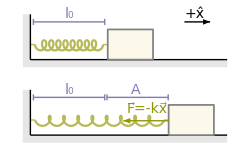

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
{t1,t2}={-1.65,25.212};
p1={1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]}/.t->t1;
p2={1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]}/.t->t2;
p3=p1+{-0.3,0};
p4=p2+{0.3,0};
x1=-3.;
x2=0.25;
y1=-2.;
x3=0.25+0.15t+1/2(0.3t+0.5Cos[2t])/.t->t2;
x4=(x3+0.3)-(2+First@p4);
centerPlot@Show[Graphics[{{FaceForm[backgroundColor2],Rectangle[p3+{-0.5,-1},p3+{0,2}],Rectangle[p3+{-0.5,-1.5},p3+{-1,-1}+{x4+12,0}]},Lighter@color2,Line[{{p1,p3},{p2,p4}}],{FaceForm[backgroundColor1],EdgeForm[{Thickness[0.005],Gray}],Rectangle[p4+{0,-1},p4+{3,1}]},{Black,Line[{{p3+{0,-1},p3+{0,2}},{p3+{0,-1},p3+{x4+11,-1}}}]}},ImageSize->250],ParametricPlot[{1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]},{t,t1,t2},PlotStyle->Lighter@color2],Graphics[{Translate[{{FaceForm[backgroundColor2],Rectangle[p3+{-0.5,-1},p3+{0,2}],Rectangle[p3+{-0.5,-1.5},p3+{-1,-1}+{x4+12,0}]},Lighter@color2,Line[{{p1,p3},{{x3,Last@p2},{x3,Last@p2}+{0.3,0}}}],{FaceForm[backgroundColor1],EdgeForm[{Thickness[0.005],Gray}],Rectangle[{x4+2,0}+p4+{0,-1},{x4+2,0}+p4+{3,1}]},{Black,Line[{{p3+{0,-1},p3+{0,2}},{p3+{0,-1},p3+{x4+11,-1}}}]}},{0,-5}]}],ParametricPlot[{0.25+0.15t+1/2(0.3t+0.5Cos[2t]),-5+1/3 Sin[2t]},{t,t1,t2},PlotStyle->Lighter@color2],Graphics[{{Arrow[#+{0,1.5}&/@{p1+{10+-0.1,0},p1+{11.5+0.1,0}}],Text[font@"+x̂",Mean[{p1+{10+-0.1,0},p1+{11.5+0.1,0}}]+{-0.2,2}]},{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{0.1,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{0.1,0}}]},Translate[{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{0.1,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{0.1,0}}]},{0,-5}],Translate[{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{x4+0.1,0}-{2.7,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{x4+0.1,0}-{2.7,0}}]},{First[p2-p1]+0.35,-5}],{color3,Text[font@"l_0",Mean[{p1,p2}]+{0,2}],Text[font@"l_0",Mean[{p1,p2}]+{0,2}+{0,-5}],Text[font["A",Italic],Mean[{p1,p2}]+{x4/2,2}+{3.4,-5}]},{color2,Thick,Arrowheads[Medium],Arrow[{{x4+2,-5.05}+p4,{x4+2,0}+p4+{-3,-5.05}}],Text[font["F⃗=-kx⃗"],{x4+4.9,-4.25}]}}]]
```

Solution
The spring is uncompressed and exerts zero force when x=0. When x is non-zero, the force exerted by the spring equals F=-k x, where the force points in the direction that restores the spring to its unstretched length. Using F=m a=m ẍ,

m ẍ=-k x

Defining the natural frequency ω^2=k/m, we can rewrite this equation as

ẍ=-ω^2x

The problem is now reduced to solving this differential equation with the initial conditions x[0]=A and ẋ[0]=0. We mention two ways to solve this differential equation.

Solution 1
We can guess a solution of the form x[t]=c_0 ⅇ^(α t) and see if it will solve our differential equation. Since ẍ=c_0 α^2 ⅇ^(α t), substituting in yields

c_0 α^2 ⅇ^(α t)=-ω^2 c_0 ⅇ^(α t)

which implies that α^2=-ω^2 or equivalently α=±ⅈ ω. Note that the c_0 factor dropped out, indicating that it truly could have been any arbitrary constant. Thus we find the two solutions

x[t]=c_1 ⅇ^(ⅈ ω t)=c_1 Cos[ω t]+ⅈ c_1 Sin[ω t]

x[t]=c_2 ⅇ^(-ⅈ ω t)=c_2 Cos[ω t]-ⅈ c_2 Sin[ω t]

As discussed in the Advanced Section above, these two solutions can be added and comprise the most general solution to this system of equations.

x[t]=(c_1+c_2)Cos[ω t]+ⅈ (c_1-c_2)Sin[ω t]

Don’t be alarmed by the fact that there is the imaginary ⅈ in this problem. It will go away when we solve for the initial conditions (c_1=A/2 and c_2=A/2) and we will obtain

x[t]=A Cos[ω t]

Technical Note
Another way you can think about this solution is to define the new constants c_3=c_1+c_2 and c_4=ⅈ (c_1-c_2); just be aware when making such transformations that you do not accidentally take away a degree of freedom from this system. In this case, this transformation is fine because c_1+c_2 and ⅈ (c_1-c_2) are not linearly dependent, so we are exchanging the two independent parameters c_1 and c_2 for the independent parameters c_3 and c_4.

Solution 2
We can solve this system directly using ẍ=(ⅆ ẋ)/ⅆt=(ⅆ ẋ)/ⅆx ⅆx/ⅆt=(ⅆ ẋ)/ⅆx ẋ. Thus

ẍ=(ⅆ ẋ)/ⅆx ẋ=-ω^2x

Separating out the variables and integrating

ẋ ⅆ ẋ=-ω^2xⅆx

1/2(ẋ)^2=-1/2 ω^2 x^2+c_1/2

where we have chosen the constant c_1/2 to get all of the 1/2 factors to simplify. Rearranging terms and integrating,

ẋ=ⅆx/ⅆt=(c_1-ω^2 x^2)^(1/2)

ⅆx/((c_1-ω^2 x^2)^(1/2))=ⅆt

1/ω ArcTan[(ω x)/((c_1-ω^2 x^2)^(1/2))]=t+c_2/ω

where we have again chosen the clever constant c_2/ω. Therefore, we find the solution

(ω x)/((c_1-ω^2 x^2)^(1/2))=Tan[ω t+c_2]

which can be solved for x to obtain

x[t]=(√c_1)/ω Sin[ω t+c_2]

As discussed in the following section, this form of the solution is exactly the same as the form x[t]=c_3 Cos[ω t]+c_4 Sin[ω t] obtained above in Solution 1. As expected, once we substitute the initial conditions we find c_1=A^2 ω^2 and c_2=π/2 and obtain

x[t]=A Cos[ω t]

just like above. □

In case you did not approve of using the word "guessing" in Solution 1, there are various general methods that you can use to find solutions to differential equations. One such method is to insert a generic power series ∑_(j=-∞)^∞ c_j x^j, obtain a relation between the c_j’s, and hope that the ultimately solution will simply from an infinite series into a nice trig function such as Sin, Cos, ⅇ...

#### Equivalence of Trig Functions

As found in the last section, when solving differential equations in multiple ways, one may often encounter multiple solutions that look seemingly different but are actually the same. In particular, the following forms are all equivalent.

x[t]=A ⅇ^(ⅈ ω t)+B ⅇ^(-ⅈ ω t)

x[t]=C Cos[ω t]+D Sin[ω t]

x[t]=E Cos[ω t+ϕ_1]

x[t]=F Sin[ω t+ϕ_2]

The two constants in any of these equations are related to the two constants in all other equations (recall that ⅇ^(ⅈ z)=Cos[z]+ⅈ Sin[z] for any z). For example,

A=1/2 (C-ⅈ D),B=1/2 (C+ⅈ D)

C=E Cos[ϕ_1],D=-E Sin[ϕ_1]

E=F,ϕ_1=ϕ_2-π/2

F=2 √(A B),ϕ_2=π+ⅈ/2 Log[A/B]

You do not need to memorize any of these relations; just understand that there are multiple forms to the most general solution for a problem.

Technical Note
As long as two solutions to an n^th order differential equation both have n independent parameters, they will be equivalent solutions.

#### Limits

A differential equation such as

ẍ=a x

has "three different solutions" depending on whether a>0, a=0, or a<0. These solutions are

x=c_1 Cos[√-a t]+c_2 Sin[√-a t] | (a<0)
x=c_3+c_4 t | (a=0)
x=c_5 ⅇ^(-√at)+c_6 ⅇ^(√a t) | (a>0)

A natural question to ask is: When a negative a approaches 0, does the solution c_1 Cos[√a t]+c_2 Sin[√a t] approach the form c_3+c_4 t? The answer is yes, and in fact, it holds for all sufficiently nice differential equations (as discussed below in Advanced Section: Linear Differential Equations).

Let’s consider a negative a and ask what happens as it approaches 0. The first thing to note is that the limit a→0 is actually very poor notation, because a has units of [time]^-2 while 0 has no units at all. It is much better to take the limit as √-a t→0 or -a t^2≪1. In this limit, we can use the Taylor series of Cos[z]≈1+O[z^2] and Sin[z]≈z+O[z^3] to obtain

x≈c_1+c_2 √a t

which we see does resemble the expected form x=c_3+c_4 t at a=0 if we define c_3=c_1 and c_4=c_2 √a. Note that this relation only holds while √-a t^2≪1, and for large enough times 1≪√-a t^2 we can no longer use the Taylor series approximation and the two forms will diverge. However, as a gets closer to 0, the range of time for which √-a t^2≪1 is valid increases, and when a=0 this range becomes infinitely long.

Of course, the same case holds in the limit of a positive a approaching zero, analogously to the case shown above!

#### Supplementary Section: Hanging from the Ceiling

Example
A spring with spring constant k hangs unstretched. A mass m is attached to the free end of the string and then released from rest. What is the resulting motion of the mass?

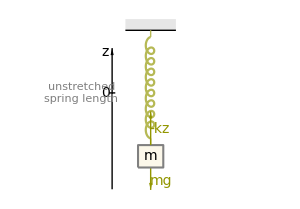

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
{t1,t2}={-1.65,25.212};
p1={1/3 Sin[2t],-1/2(0.3t+0.5Cos[2t])}/.t->t1;
p2={1/3 Sin[2t],-1/2(0.3t+0.5Cos[2t])}/.t->t2;
p3=p1+{0,0.3};
p4=p2+{0,-0.3};
x1=-3.;
x2=0.25;
y1=-2.;
centerPlot@Show[Graphics[{Line[{p3+{-2,0},p3+{2,0}}],{FaceForm[backgroundColor2],Rectangle[p3+{-2,0},p3+{2,0.5}]},Lighter@color2,Line[{{p1,p3},{p2,p4}}]},ImageSize->300],ParametricPlot[{1/3 Sin[2t],-1/2(0.3t+0.5Cos[2t])},{t,t1,t2},PlotStyle->Lighter@color2],Graphics[{{Line[{{x1-x2,y1},{x1+x2,y1}}],Text[font@"0",{x1-x2-0.3,y1}],Text[font["z",Italic],{x1-0.52,-0.18}],Gray,Text[Grid[List/@(font[#,12]&/@{"unstretched","spring length"}),Spacings->{0,0.1}],{x1-x2-2.2,y1}],White,Text[Grid[List/@(font[#,12]&/@{"unstretched","spring length"}),Spacings->{0,0.1}],{-(x1-x2-2.2),y1}]},{Arrowheads[0.04],Arrow[{{#,-6.3},{#,0}}&@x1]},{FaceForm[backgroundColor1],EdgeForm[{Thickness[0.005],Gray}],Rectangle[p4+{-1,0},p4+{1,-1}]},Text[font["m",Italic],p4+{0,-0.5}],{color2,Thick,Arrowheads[Medium],Arrow[{{p4+{0,-1},p4+{0,-2}},{p4+{0,0},p4+{0,1.5}}}],Text[font["mg",Italic],p4+{0.85,-1.9},{0,-1}],Text[font["-kz",Italic],p4+{0.7,0.4},{0,-1}]}}]]
```

Solution
Denote the position of the unstretched spring as z=0. The equilibrium position (where the gravitational force m g and the spring force -k z sum to zero) occurs at z_0=-(m g)/k. The force at any height is given by

m z̈=F=-k z-m g=-k (z-z_0)

Since z_0 is a constant, (ż)_0=(z̈)_0=0 so we can write the above equation

m OverDoubleDot[(z-z_0)]=-k (z-z_0)

which is harmonic motion in the variable z-z_0. Thus, the mass will oscillate about the equilibrium position z=z_0 (you can prove this formally by changing variables to z̃=z-z_0). Setting ω_0=(k/m)^(1/2), the solution is given by

z[t]-z_0=c_1 Sin[ω_0 t]+c_2 Cos[ω_0 t]

Since the mass was released from rest at t=0, the initial conditions are z[0]=0 and ż[0]=0 so that c_1=0 and c_2=-z_0,

z[t]=z_0(1- Cos[ω_0 t])

so the mass will oscillate between z=0 and z=2 z_0=-(2m g)/k.

Note that this frequency of oscillation ω_0 is identical to that for a horizontal spring. This might seem surprising, but gravity exerts a constant force m g, which serves to simply shift the oscillations of the spring from being centered on z=0 to z=z_0. Because the force exerted by the spring is linear, the resulting oscillations about z=z_0 are identical to the oscillations for the horizontal spring about z=0. □

#### Advanced Section: Time Reversal

Often times in classical mechanics you can get a quick answer to a question simply by looking at the system and qualitatively understanding its motion. Building up your intuition allows you to double check your work (i.e. the three page long derivation you just did) very quickly. We often do this by checking limiting cases, but if you can visualize the motion in a problem you open up even cooler ways of checking your work.

Example
Consider a vertical pendulum with spring constant k. A mass m is released from rest at the unstretched spring height. What is the highest point the mass will reach? What is the lowest point the mass will reach?

Solution
Without knowing anything about the motion of the mass, we can answer this question quite simply. All we need to visualize in our heads is that gravity will pull the mass downwards, and eventually the spring will pull up strongly enough to stop the decent and bring the mass up again. We can suspect that oscillations will occur but the details don’t matter.

Instead, let’s focus in on a very brief initial time period t=0→t=δ,t when the mass first begins to fall. Gravity will pull the mass downwards. Now, let’s reverse time and focus on the time period t=δ,t→t=-δ,t! The mass is going to swing upwards to z=0 at t=0. Then what? Physics applies just the same with forward time as with reverse time: therefore the mass will once again be pulled downwards by gravity.

Therefore, the highest point that the mass will achieve is z=0. Awesome!

Of course, conservation of energy tells us that the mass will definitely reach its initial height again. Also, conservation of energy very easily tells us that the lowest point that mass achieves occurs when it has traded all of its potential energy into the spring’s potential energy (with zero velocity), 0=m g z_min+1/2 k z_min^2 which yields z_min=-(2 m g)/k. Done! □

Example
Two identical blocks of mass m lie on a frictionless horizontal table. They are connected by a massless spring with spring constant k and are initially at rest (i.e. with the spring unstretched with length l_0). Someone comes and kicks the left mass, imparting it with a velocity v_0 directly upwards. In the ensuing motion of the two masses, what is the greatest length and the least length that the spring achieves?

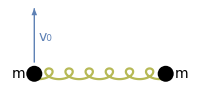

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
centerPlot@Show[Graphics[{color1,Thick,Arrowheads[Medium],Arrow[{{-1,0.7},{-1,4.1}}],Text[font["v_0"],{-0.3,2.3}]},ImageSize->200],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r],Text[font["m",Italic],pt1+{-1,0}],Text[font["m",Italic],pt2+{1.,0}]}]]
```

Solution
This problem is greatly simplified if we step into the (inertial) reference frame moving at velocity v_0/2. In this case, the problem is symmetric, with both masses moving at velocity v_0/2 in opposite direction at t=0, and the center of mass does not move (by symmetry).

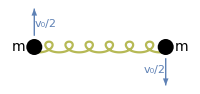

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
centerPlot@Show[Graphics[{color1,Thick,Arrowheads[Medium],Arrow[{{-1,0.7},{-1,2.4}}],Text["v_0/2",{-0.3,1.45}],Arrow[{{7.2,-0.7},{7.2,-2.4}}],Text["v_0/2",{6.5,-1.45}]},ImageSize->200],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r],Text[font["m",Italic],pt1+{-1,0}],Text[font["m",Italic],pt2+{1.,0}]}]]
```

Consider the brief initial time period t=0→t=δ,t. In this case, the masses will both move forward, and they will both work to stretch the spring out (after all, there is no centripetal force to keep them moving in a circle). If we now reverse time and consider the brief time period t=δ,t→t=-δ,t. The masses will swing back to the origin spring length and their original velocities (although now their velocities point in the opposite directions), and we once again expect that the masses will swing out and stretch the spring. Therefore, the minimum length of the spring must equal the initial length of the spring l_0! Awesome!!!

What is the largest length that the spring achieves? The only force in the problem is tension, so if we consider the angular momentum about the center of mass then there are no torques and angular momentum is conserved. At t=0, the angular momentum for the two masses equals 2m v_0/2 l_0/2=(m v_0 l_0)/2 while at its further point the angular momentum equals 2m v_f l_f/2=m v_f l_f where we have used the symmetry of the problem to determine that both masses will have the same final velocity v_f and be the same length l_f/2 away from the center of the spring. Thus

(m v_0 l_0)/2=m v_f l_f

Conservation of energy tells us that

2(1/2 m (v_0/2)^2)=2(1/2 m v_f^2)+1/2 k (l_f-l_0)^2

These above two equations can be solved for l_f, although the actual exact answer is horribly messy!

This was asked on the Qualifying Exams for Physics Graduate students. Of course, in that exam, they led you through a much more complicated method, taking the Lagrangian and doing all sort of crazy computations to determine the motion of the masses as a function of time; but if you just keep your head, then you can answer these questions with very little effort! □

#### Angled Rails

Example
Two particles of mass m are constrained to move along two rails that make an angle of 2θ with respect to each other, as shown below. They are connected by a spring with spring constant k and unstretched spring length 2 x_0 Sin[θ] where x_0 is the distance along the rails from the base point to one of the masses. Find the frequency of oscillations for the motion where the spring remains parallel to the position (as shown below) if:
1. The two rails are horizontal, so that gravity does not affect the motion
2. The two rails are vertical and gravity does affect the system

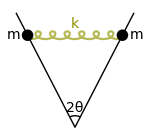

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
pt3=Mean[{pt1,pt2}]+{0,-8};
{pt4,pt5}={{#,Fit[{pt1,pt3},{1,x},x]/.x->#}&[-2],{#,Fit[{pt2,pt3},{1,x},x]/.x->#}&[8.2]};
centerPlot@Show[Graphics[{Line[{pt4,pt3,pt5}],Circle[pt3,1,{ArcTan@@(pt2-pt3),ArcTan@@(pt1-pt3)}],Text[font["2θ"],pt3+{0,1.7}],color2,Text[font["k",Italic],pt3+{0,9}]},ImageSize->150],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r],Text[font["m",Italic],pt1+{-1.2,0}],Text[font["m",Italic],pt2+{1.2,0}]}]]
```

Solution
Denote x to be the distance from the rail intersection at the bottom to a point mass, so that the length of the spring equals 2(x-x_0)Sin[θ] and the spring force is given by -2k (x-x_0)Sin[θ]. Note that the component of the spring force along the rails equals -2k (x-x_0)Sin[θ]^2.

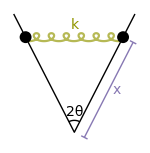

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
pt3=Mean[{pt1,pt2}]+{0,-8};
{pt4,pt5}={{#,Fit[{pt1,pt3},{1,x},x]/.x->#}&[-2],{#,Fit[{pt2,pt3},{1,x},x]/.x->#}&[8.2]};
n1=Normalize[pt2-pt3];
n2={1,-1}*Reverse@n1;
r2=0.3;
centerPlot@Show[Graphics[{Line[{pt4,pt3,pt5}],Circle[pt3,1,{ArcTan@@(pt2-pt3),ArcTan@@(pt1-pt3)}],Text[font["2θ"],pt3+{0,1.7}],color2,Text[font["k",Italic],pt3+{0,9}],color3,Line[{0.95n2+#&/@{pt3,pt2},{(0.95-r2)n2+pt3,(0.95+r2)n2+pt3},{(0.95-r2)n2+pt2,(0.95+r2)n2+pt2}}],Text[font["x",Italic],Mean[0.95n2+#&/@{pt3,pt2}]+{0.7,0}]},ImageSize->150],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r]}]]
```

1. When the rails are horizontal, the motion of the system is dictated purely by the spring force, since gravity points into the page and the normal force only serves to keep the masses on the rails. Thus, F=m a=m ẍ for the system yields

m ẍ=-2k (x-x_0)Sin[θ]^2

Using the natural frequency ω^2=k/m, we can rewrite this as

ẍ=-2 ω^2 (x-x_0)Sin[θ]^2

OverDoubleDot[(x-x_0)]=-2 ω^2 (x-x_0)Sin[θ]^2

where in the last step we used ẍ=OverDoubleDot[(x-x_0)] since the time derivative of the constant x_0 is zero. If we define

(ω̃)^2=2 ω^2 Sin[θ]^2

then Equation (TextNumbered) reduces to

OverDoubleDot[(x-x_0)]=-(ω̃)^2 (x-x_0)

which we know has the solution

x[t]-x_0=c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

or equivalently

x[t]=x_0+c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

Therefore, the frequency of oscillations is given by

ω̃=((2k)/m)^(1/2)Sin[θ]

2. If the rails are vertical and gravity is in play (with a component m g Cos[θ] along the rails), the sum of the forces equals

m ẍ=-m g Cos[θ]-2k (x-x_0)Sin[θ]^2

Using the frequence ω^2=k/m and reorganizing this equation,

ẍ=-g Cos[θ]-2 ω^2 (x-x_0)Sin[θ]^2

OverDoubleDot[(x-x_0)]+2 ω^2 (x-x_0)Sin[θ]^2=-g Cos[θ]

where, as above, we have used ẍ=OverDoubleDot[(x-x_0)]. If the right-hand side was 0, the solution to this differential equation is given by Equation (TextNumbered). How do we modify this solution to satisfy the current differential equation with the gravity term? As always, we start with the simplest possible guess: can we add a constant to Equation (TextNumbered) and get a valid solution for Equation (TextNumbered)? Indeed, we can, as exhibited by

x[t]=x_0-(g Cos[θ])/(2 ω^2 Sin[θ]^2)+c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

Therefore, as we found in the first solution for horizontal rails, the frequency of oscillations is given by

ω̃=((2k)/m)^(1/2)Sin[θ]

This frequency is unchanged between the two cases because gravity exerts a constant force which serves to only shift the equilibrium location of the oscillations (shifting it from being centered on x_0 in the horizontal case to being shifted around x_0-(g Cos[θ])/(2 ω^2 Sin[θ]^2) for the vertical case), but because the spring force is linear the oscillations about this new equilibrium are identical in both cases. □

#### Real World Applications

So what have we learned so far? At first blush, it might not seem like much. We covered the motion of a mass on a spring and found out that this mass oscillates periodically. But it is easy to extend this simple analysis to many objects that we deal with in our daily lives. For example, a drum can be modeled as an array of masses connected by springs, where each mass oscillates into and out of the board.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

When you analyze such systems, you find that the particles collectively undergo what are called normal modes - it is essentially doing the wave on a large scale across the entire object. But there are many forms of the wave, and there are many normal modes. For a circular drum, the most prevalent normal modes are shown below. The fundamental mode (top-left) is exactly what you expect - the center of the drum goes up and down. But the other modes are weird, cool, and bizarre, with parts of the drum moving up while other parts move down (and then the two regions switch).

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6];
centerPlot@Labeled[Grid[Partition[Table[Plot3D[funs[[i]],{x,y}∈Disk[],PlotRange->All,PlotTheme->"Minimal"],{i,Length[vals]}],3]],font@"Normal Modes of a Drum\n",Top]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-Normal Modes of a Drum

The drum is a great system, because its circular geometry is particularly simple, and hence the normal modes can be solved analytically, but if you are willing to go to numerics, you can solve the normal modes of any shape you want. For example, suppose you order a drum shaped like...a Pikachu! No problem!!! It takes 2 lines of Mathematica code to find the normal modes of this drum. From these normal modes, you can determine what the Pikachu drum will sound like (surprisingly, it does not emit a “pi-ka-chu” sound when struck).

```mathematica
img=Entity["Pokemon","Pokedex0025:Pikachu"]["Image"];
mesh=ImageMesh[Binarize[img,0]];
{vals,funs}=NDEigensystem[{Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈mesh,6];
centerPlot@Labeled[Grid[{{Show[img,ImageSize->150],Grid[Partition[Table[Plot3D[funs[[i]],{x,y}∈mesh,PlotRange->All,PlotTheme->"Minimal",ImageSize->150],{i,Length[vals]}],3]]}},Spacings->1],font@"Normal Modes of Pikachu\n",Top]
```

-Graphics- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-Normal Modes of Pikachu

Next, let’s talk about the normal modes of a rectangular plate. Just like in the drum example above, for each normal mode (except the fundamental node), some part of the rectangle will oscillate up while another part goes down, which necessarily implies that there is always some part of the rectangle that is not moving at all throughout the entire normal mode motion. This beautiful animation lets you visualize what these stationary contours look like.

Here is another extremely bizarre example. Five metronomes are ticking with the same frequency but at different phases. The metronomes are coupled together by putting all five of them on top of a wooden plank laid on two soda cans. Every time a metronome oscillates from side to side, it will make the wooden plank roll in the opposite direction (to keep the center of mass of the entire system stationary), and the other metronomes will feel that motion through the plank. Quite surprisingly, after a few seconds have elapsed, the metronomes are in sync!

It seems that the force imprinted by the motion of each metronome on the plank becomes the source of a forced oscillator for each of them (a type of self-forced system), and the steady state is one where all of the metronomes oscillating in phase and frequency - the equivalent of a resonant state. Without the cans, the reaction of each metronome is counteracted by the fixed support (desk) and there’s no coupling among them.

There are many phenomenon that we encounter every day that are all based on oscillations, or can be modeled as oscillators. But let us take a step back and talk about physics. The mass on a spring - also known as the simple harmonic oscillator - is the single most important model in all of physics! I am not kidding. This system shows up repeatedly in every subject from quantum mechanics to condensed matter to quantum field theory. So believe it or not, in solving these simple problems today, we took a rather large step to understand how much of the universe works.

### Advanced Section: Linear Differential Equations

#### Overview

A linear differential equation is a differential equation that has the form

(ⅆ^n y)/(ⅆ t^n)+A_1[t](ⅆ^(n-1)y)/(ⅆ t^(n-1))+···+A_(n-1)[t]ⅆy/ⅆt+A_n[t]y=f[t]

where f[t] and the A_j[t] are any functions of t and n is the smallest possible integer that permits this form. Such a linear differential equation is said to have order n (i.e. the index of the highest derivative of y involved). A linear equation is said to be homogeneous if f[t]=0 and non-homogeneous if f[t]≠0.

Some useful properties of linear differential equations are:
1. Given two solutions y_1[t] and y_2[t] of a homogeneous linear differential equations, the combination c_1 y_1[t]+c_2 y_2[t] is also a solution to the same linear differential equation
2. An n^th order homogeneous linear differential equations will have n linearly independent solutions. Said another way, if you find a solution to a homogeneous linear differential equation that has n different parameters y[c_1,c_2... c_n] where varying any of the c_j’s is still a solution, then you have found the most general solution to this differential equation (i.e. every solution to this differential equation will equal y[c_1,c_2... c_n] for some value of c_1,c_2... c_n).
3. Given any solution y_(non-homogenous) to an n^th order non-homogeneous linear differential equation and the most general solution y_homogenous[c_1,c_2... c_n] to this same linear differential equation with f[t] set to 0, the most general solution for this non-homogeneous linear differential equation is y_(non-homogenous)+y_homogenous[c_1,c_2... c_n].

What this means for us is that when we encounter a homogeneous 2^nd order linear differential equation (such as m ẍ=-k x, which we will encounter for the spring force in the next section), once we have found a solution with two independent parameters (in this case, x[t]=c_1 Cos[(k/m)^(1/2)t]+c_2 Sin[(k/m)^(1/2)t] where c_1 and c_2 are our two independent parameters), then we know that we have found the most general solution for the system.

Why do we need these two free parameters? Given a particular value for x[0] and ẋ[0], the values of c_1 and c_2 can be determined to match these initial conditions.

#### Linearity of Solutions

Theorem
Consider a linear differential equation that depends on a parameter a with the form

x^(n)[t]+f_(n-1)[a]x^(n-1)[t]+f_(n-2)[a]x^(n-2)[t]+···f_0[a]x[t]=g_0[a]

where the f_j[a] and g_0[a] are all continuous functions of a. Then the solution x_a[t] will be a continuous function in a.

Proof
(This proof can naturally be extended to two or more parameters. We suppress the t dependence of all functions throughout.)

Let x_a be a solution to the above differential equation, and let us consider what happens to the soution when we vary a→a+ⅆa. The new differential equation becomes

x^(n)+(f_(n-1)[a]+f_(n-1)'[a]ⅆa)x^(n-1)+···(f_0[a]+f_0'[a]ⅆa)x+O[ⅆa]^2=g_0[a]+g_0'[a]ⅆa

Let us write the new solution to this differential equation as

x_(a+ⅆa)=(x_a+h_0)+h_1 ⅆa+O[ⅆa]^2

where we have explicitely pulled out the solution when ⅆa→0. Our goal will be to show that h_0=0, which will imply that for an infinitesimal change a→a+ⅆa, the change in the solution is x_a→x_a+h_1 ⅆa, and therefore the solution x_a to the differential equation is continuous in a.

Substituting x=x_(a+ⅆa) into the above differential equation and grouping together all terms of order (ⅆa)^0,

(x_a^(n)+h_0^(n)+f_(n-1)[a](x_a^(n-1)+h_0^(n-1))+···+f_0[a](x_a+h_0))+O[ⅆa]^1=g_0[a]

where we have dropped the order (ⅆa)^1 terms because the left-hand side must equal the right hand side for each order of ⅆa independently! By definition, x_a solves the original differential equation which implies

h_0^(n)+f_(n-1)[a]h_0^(n-1)+···+f_0[a]h_0+O[ⅆa]^1=0

Since we are looking for a specific solution (i.e. a non-homogeous solution), the desired answer is h_0=0. Note that we are not looking for the homogenous solution h_0=x_a, which has already been accounted for when we specifically wrote the solution as x_(a+ⅆa)=(x_a+h_0)+h_1 ⅆa+O[ⅆa]^2.

Therefore, we have shown that x_(a+ⅆa)-x_a is of order (at least) ⅆa, which implies that the solution x_a is continuous in a, as desired. □

#### Basic Example

To dig deeper into the above Theorem, consider the case

ẍ+f[a]x=0

where f[a] is a continuous function in a. We know that the solution equals

x_a=c_1 Cos[√f[a]t]+c_2 Sin[√f[a]t]

when we vary a→ⅆa, the solution becomes

x_(a+ⅆa)=(c_1 Cos[√f[a]t]+c_2 Sin[√f[a]t])+(-c_1Sin[√f[a]t]+c_2 Cos[√f[a]t])(f'[a]t)/(2 √f[a])ⅆa+O[ⅆa]^2

when we substitute this back into the differential equation ẍ+(f[a]+f'[a]ⅆa)x=0, we do indeed find that all terms of order (ⅆa)^0 and (ⅆa)^1 have canceled, leaving us with

OverDoubleDot[x_(a+ⅆa)]+(f[a]+f'[a]ⅆa)x_(a+ⅆa)=(-c_1Sin[√f[a]t]+c_2 Cos[√f[a]t])(t f'[a]^2)/(2 √f[a])(ⅆa)^2=O[ⅆa]^2

as expected!

## Mathematica Initialization

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter[ColorData[97][7],0.2]};
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1,backgroundColor2}={RGBColor[0.99, 0.97432, 0.91748],RGBColor[0.9, 0.9, 0.9]};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
$Assumptions=By>0&&Bz>0&&c>0&&0<ϕ<2π&&0≤ψ≤2π;
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}},{base,base+size{-0.05,-0.05}}}],Text[font@"x̂",base+size{0.12,0}],Text[font@"ŷ",base+size{0,0.12}],Text[font@"ẑ",base+size{-0.06,-0.065}]}
```